## Getting started

### Imports and definitions

```mathematica
Get[NotebookDirectory[]<>"/AmadoTemp/DTQW.wl"]
Get["/home/jadeleon/Documents/quantum_chaotic_channels/QMB.wl"]
<<MaTeX`

(*MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];*)
```

### Initializations

```mathematica
tMax=5;
```

```mathematica
InitializeDTQW[2,tMax]
MakeCoin[1/2.,0,0];
MakeShift[];
MakeUnitary[];
```

```mathematica
plotlist={};
```

### Definiendo variables

```mathematica
IndigoC=RGBColor["#729cfc"];
AquaC=RGBColor["#4bd7e5"];
DeepBlueC=RGBColor["#1e2c88"];
```

```mathematica
qlabels=Import[NotebookDirectory[]<>#,{"PDF","PageGraphics"},
ImageSize->{Automatic,16}
][[1]]&/@{"Labels_pos.pdf","Labels_prob.pdf"};
clabels=Import[NotebookDirectory[]<>#,{"PDF","PageGraphics"},
ImageSize->{Automatic,16}
][[1]]&/@{"Labels_pos.pdf","Labels_probc.pdf"};
plotargs={
BaseStyle->{FontFamily->"LM Roman 12",FontSize->15},
PlotRange->All,
Axes->False,
Frame->True,
Mesh->All,
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,Opacity[0.5]]
};
```

Import::nffil: File /home/jadeleon/Documents/quantum_walks/Labels_pos.pdf not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Import::nffil: File /home/jadeleon/Documents/quantum_walks/Labels_prob.pdf not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Import::nffil: File /home/jadeleon/Documents/quantum_walks/Labels_pos.pdf not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Import::nffil: File /home/jadeleon/Documents/quantum_walks/Labels_probc.pdf not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

```mathematica
TeXLabel[tlist_List]:=MaTeX[
"\\begin{gathered}\n"<>Fold[
StringJoin[#1,"\\\\\n",#2]&,ToString@StringForm["\\text{``}",#]&/@tlist
]<>"\n\\end{gathered}",
FontSize->14,
Magnification->1.3,
"Preamble"->{"\\usepackage{physics}"}
]
```

## Diferentes estados iniciales

## (+_y)_c⊗0_p

```mathematica
ψ0=VectorState[{{1/Sqrt[2],0,0},{ⅈ/Sqrt[2],1,0}}]
```

VectorState[{{1/(√2),0,0},{ⅈ/(√2),1,0}}]

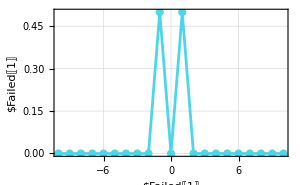
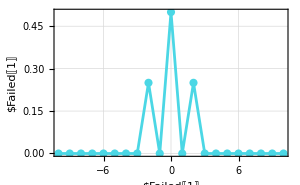
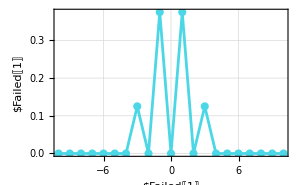
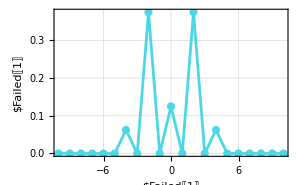
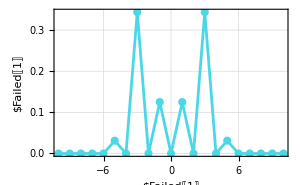
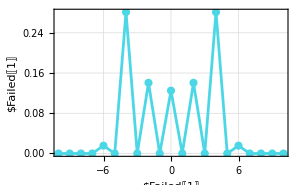
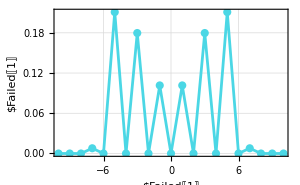
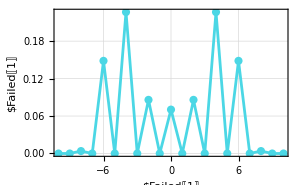

```mathematica
tMax=10;
Table[
InitializeDTQW[2,2*tMax+1];MakeCoin[1/2.,0,0];MakeShift[];MakeUnitary[];
probs=Abs[Diagonal[MatrixPartialTrace[Dyad[Flatten[DTQW[ψ0,t]]],1,{2,2*tMax+1}]]];
ListLinePlot[{Range[-tMax,tMax],probs}ᵀ,ImageSize->300,
plotargs,
PlotLabel->TeXLabel[{"Pasos: "<>ToString[t]}],
FrameLabel->clabels,
PlotStyle->AquaC
],
{t,tMax}]
```

## 0_c⊗0_p

```mathematica
ψ0=VectorState[{{1.,0,0}}]
```

VectorState[{{1.,0,0}}]

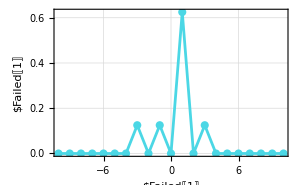
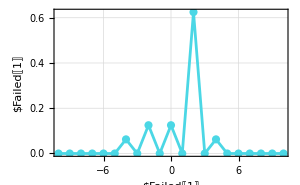
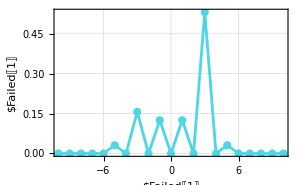
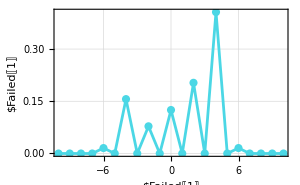
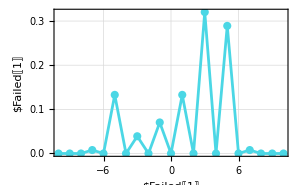
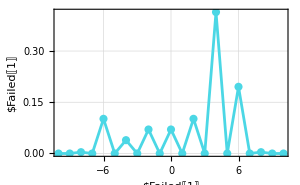
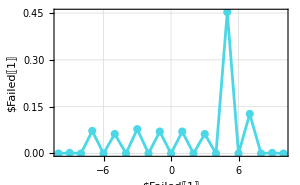
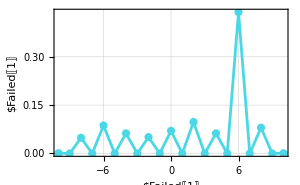
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
tMax=10;
Table[
InitializeDTQW[2,2*tMax+1];MakeCoin[1/2.,0,0];MakeShift[];MakeUnitary[];
probs=Abs[Diagonal[MatrixPartialTrace[Dyad[Flatten[DTQW[ψ0,t]]],1,{2,2*tMax+1}]]];
ListLinePlot[{Range[-tMax,tMax],probs}ᵀ,ImageSize->300,
plotargs,
PlotLabel->TeXLabel[{"Pasos: "<>ToString[t]}],
FrameLabel->clabels,
PlotStyle->AquaC
],
{t,tMax}]
```

## 1_c⊗0_p

```mathematica
ψ0=VectorState[{{1.,1,0}}]
```

VectorState[{{1.,1,0}}]

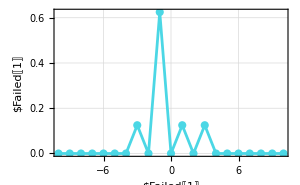
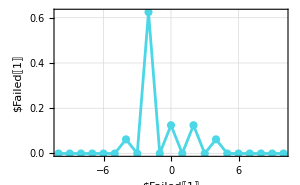
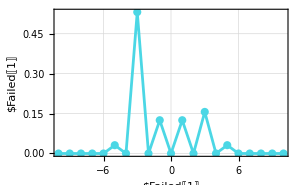
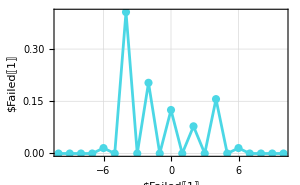
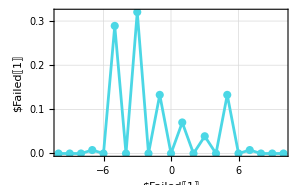
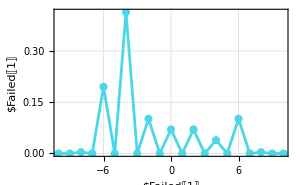
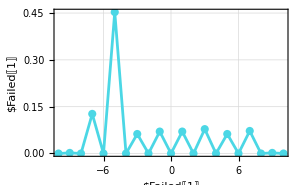
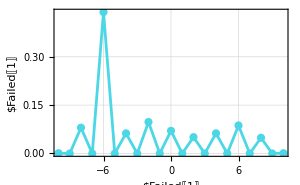
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
tMax=10;
Table[
InitializeDTQW[2,2*tMax+1];MakeCoin[1/2.,0,0];MakeShift[];MakeUnitary[];
probs=Abs[Diagonal[MatrixPartialTrace[Dyad[Flatten[DTQW[ψ0,t]]],1,{2,2*tMax+1}]]];
ListLinePlot[{Range[-tMax,tMax],probs}ᵀ,ImageSize->300,
plotargs,
PlotLabel->TeXLabel[{"Pasos: "<>ToString[t]}],
FrameLabel->clabels,
PlotStyle->AquaC
],
{t,tMax}]
```

## Estado que no es el entrelazado

## 1/2(0+ⅈ1)⊗(-20+20)

```mathematica
ψ0=VectorState[{{1/2,0,-20},{1/2,0,20},{ⅈ/2,1,-20},{ⅈ/2,1,20}}]
```

VectorState[{{1/2,0,-20},{1/2,0,20},{ⅈ/2,1,-20},{ⅈ/2,1,20}}]

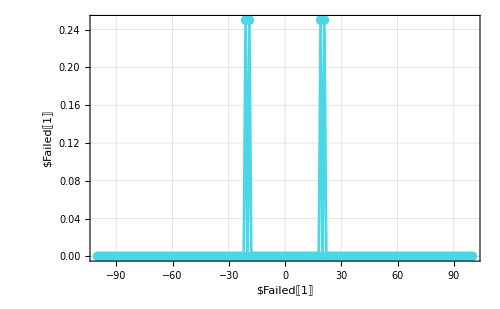
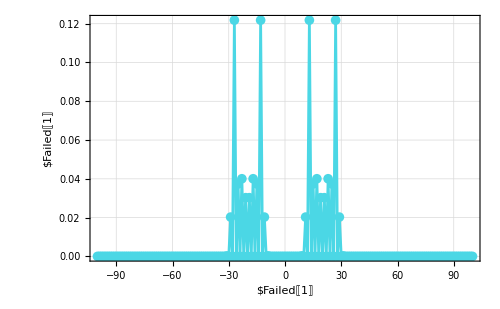
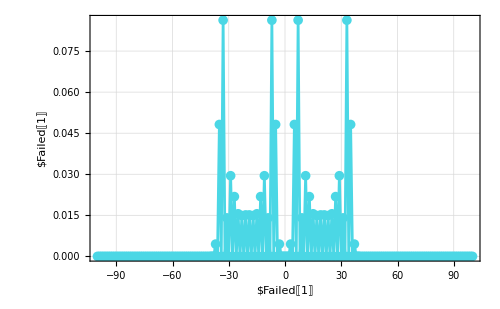
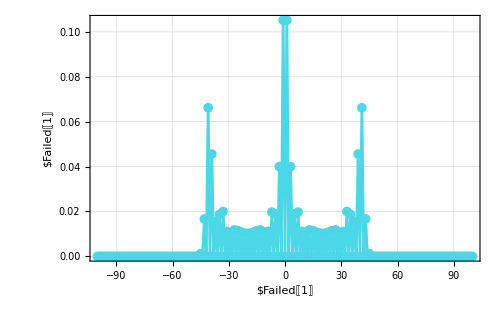
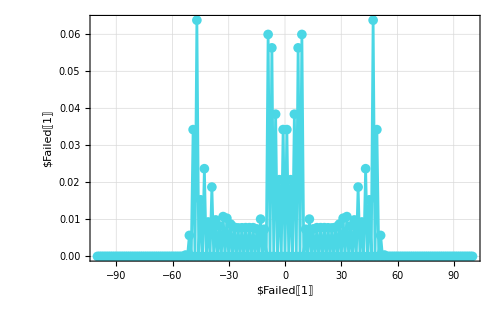
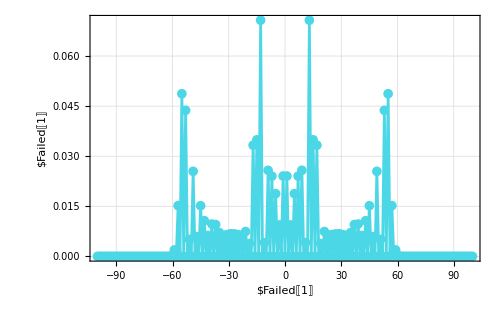
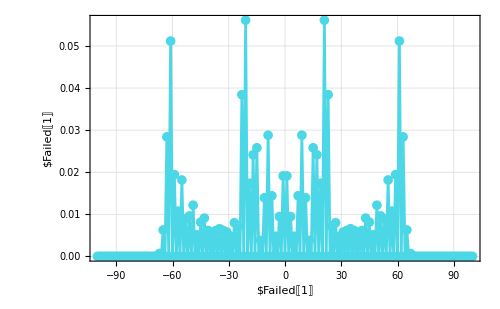
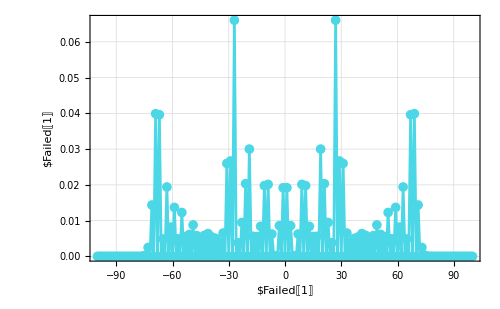

```mathematica
t=tMax=100;
Table[
InitializeDTQW[2,2*tMax+1];MakeCoin[1/2.,0,0];MakeShift[];MakeUnitary[];
probs=Abs[Diagonal[MatrixPartialTrace[Dyad[Flatten[DTQW[ψ0,t]]],1,{2,2*tMax+1}]]];
ListLinePlot[{Range[-tMax,tMax],probs}ᵀ,ImageSize->500,
plotargs,
PlotLabel->TeXLabel[{"Pasos: "<>ToString[t]}],
FrameLabel->clabels,
PlotStyle->AquaC
],
{t,1,100,10}]
```

## Ver si la gaussiana se está ensanchando*

```mathematica
ψ0=VectorState[{{1/Sqrt[2],0,0},{ⅈ/Sqrt[2],1,0}}]
```

VectorState[{{1/(√2),0,0},{ⅈ/(√2),1,0}}]

```mathematica
{tMax,pPhaseFlip}={150,0.5}
```

{150,0.5}

```mathematica
?DTQW2wDecoherence
```

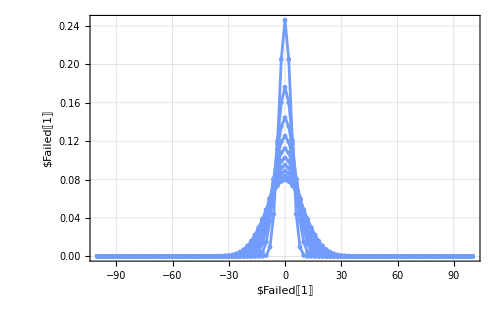

```mathematica
ListLinePlot[
Table[
probs=Abs[Diagonal[MatrixPartialTrace[DTQW2wDecoherence[ψ0,1-pPhaseFlip,t],1,{2,201}]]](*DTQW2wDecoherence sólo funciona con t=100??*);
{Range[-100,100,2],probs[[;;;;2]]}ᵀ,
{t,10,100,10}],
ImageSize->500,
plotargs,
PlotLabel->TeXLabel[{ToString[t]<>" pasos. Estado inicial: $\\ket{+_y}\\otimes\\ket{0}$","Phase flip error = "<>ToString[pPhaseFlip]}],
FrameLabel->qlabels,
PlotStyle->IndigoC
]
```

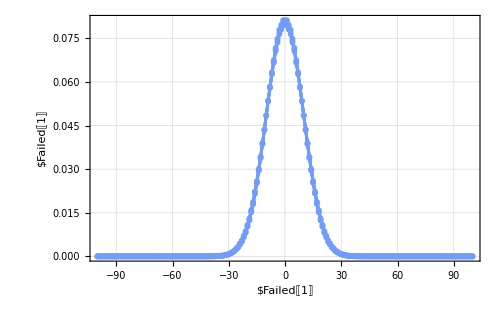

```mathematica
ListLinePlot[
Table[
probs=Abs[Diagonal[MatrixPartialTrace[DTQW2wDecoherence[ψ0,1-pPhaseFlip,t],1,{2,201}]]](*DTQW2wDecoherence sólo funciona con t=100??*);
{Range[-100,100,2],probs[[;;;;2]]}ᵀ,
{t,96,100,2}]~Join~Table[
probs=Abs[Diagonal[MatrixPartialTrace[DTQW2wDecoherence[ψ0,1-pPhaseFlip,t],1,{2,201}]]](*DTQW2wDecoherence sólo funciona con t=100??*);
{Range[-99,99,2],probs[[2;;-2;;2]]}ᵀ,
{t,95,99,2}],
ImageSize->500,
plotargs,
PlotLabel->TeXLabel[{ToString[t]<>" pasos. Estado inicial: $\\ket{+_y}\\otimes\\ket{0}$","Phase flip error = "<>ToString[pPhaseFlip]}],
FrameLabel->qlabels,
PlotStyle->IndigoC
]
```